-Graphics3D-

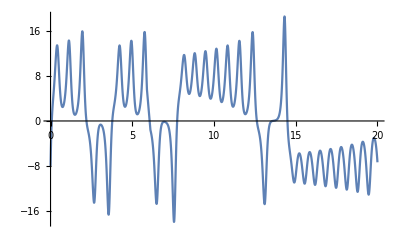

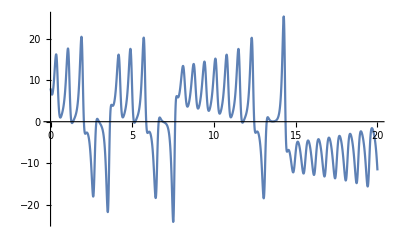

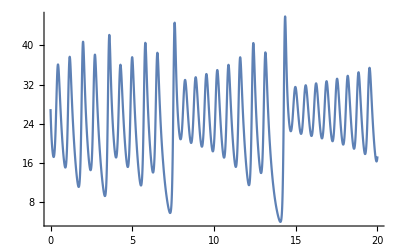

```mathematica
f1[y1_,y2_]:=σ(y2-y1);
f2[y1_,y2_,y3_]:=-y1 y3+r y1-y2;
f3[y1_,y2_,y3_]:=y1 y2-b y3;

σ=10; b=8/3; r=28;
point1={-8,8,r-1};
point2={10,-100,1};
point3={-30,30,r-30};
tmax=20;

sol1=NDSolve[{
y1'[t]==f1[y1[t],y2[t]],
y2'[t]==f2[y1[t],y2[t],y3[t]],
y3'[t]==f3[y1[t],y2[t],y3[t]],
y1[0]==point1⟦1⟧,
y2[0]==point1⟦2⟧,
y3[0]==point1⟦3⟧
},
{y1,y2, y3},
{t,0,tmax}
]⟦1⟧;

plot=ParametricPlot3D[
{y1[t], y2[t], y3[t]} /. sol1,
{t,0,tmax}, PlotRange->All
]

Plot[y1[t]/.sol1,{t,0 ,tmax}]
Plot[y2[t]/.sol1,{t,0 ,tmax}]
Plot[y3[t]/.sol1,{t,0 ,tmax}]
```

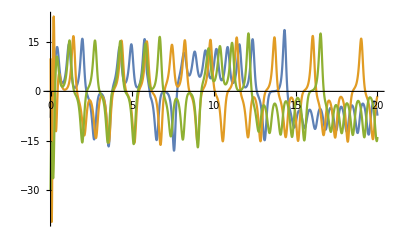

```mathematica
getSol[{y10_,y20_,y30_}]:=
Module[{},
sol=NDSolve[{
y1'[t]==f1[y1[t],y2[t]],
y2'[t]==f2[y1[t],y2[t], y3[t]],
y3'[t]==f3[y1[t],y2[t], y3[t]],
y1[0]==y10,
y2[0]==y20,
y3[0]==y30
},
{y1,y2,y3},
{t,0,tmax}
]⟦1⟧;
sol
]

Plot[
Evaluate[{
{y1[t]}/.getSol[point1],
{y1[t]}/.getSol[point2],
{y1[t]}/.getSol[point3]
}]
,{t,0,tmax}]
```

```mathematica
plot2=ParametricPlot3D[
Evaluate[{
{y1[t],y2[t],y3[t]}/.getSol[point1],
{y1[t],y2[t],y3[t]}/.getSol[point2],
{y1[t],y2[t],y3[t]}/.getSol[point3]
}],
{t, 0, tmax}, PlotRange->All]
```

-Graphics3D-

```mathematica
statPoint=Solve[{
f1[y1,y2]==0,
f2[y1,y2,y3]==0,
f3[y1,y2,y3]==0
},
{y1,y2,y3}];

plotStat1=Graphics3D[{Red,PointSize[Large], Point[{y1, y2, y3} /. statPoint[[1]]]}];
plotStat2=Graphics3D[{Blue,PointSize[Large], Point[{y1, y2, y3} /. statPoint[[2]]]}];
plotStat3=Graphics3D[{Black,PointSize[Large], Point[{y1, y2, y3} /. statPoint[[3]]]}];

Show[{plot2, plotStat1, plotStat2, plotStat3}, PlotRange->All]
```

-Graphics3D-

```mathematica
J=D[{
f1[y1, y2],
f2[y1,y2,y3],
f3[y1,y2,y3]},
{{y1,y2,y3}}];
eigenvalues=Eigenvalues[J];
e1=eigenvalues/.statPoint[[1]]//N
e2=eigenvalues/.statPoint[[2]]//N
e3=eigenvalues/.statPoint[[3]]//N
```

{-22.8277,-2.66667,11.8277}

{-13.8546,0.0939556-10.1945 ⅈ,0.0939556+10.1945 ⅈ}

{-13.8546,0.0939556-10.1945 ⅈ,0.0939556+10.1945 ⅈ}

```mathematica
ParametricPlot3D[
Evaluate[{
{y1[t], y2[t], y3[t]} /. getSol[({y1,y2,y3} /.statPoint⟦1⟧) + 10^-10]
}],
{t,0,tmax},PlotRange->All]
```

-Graphics3D-

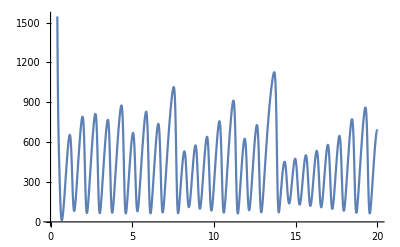

```mathematica
point4={100, 100, 100};

V[t_]:=({y1[t]}/.getSol[point4])^2+({y2[t]}/.getSol[point4])^2+(({y3[t]}/.getSol[point4])-σ-r)^2;

Plot[Evaluate[V[t]], {t,  0, tmax}]
```